# practicals 1 19/01/23

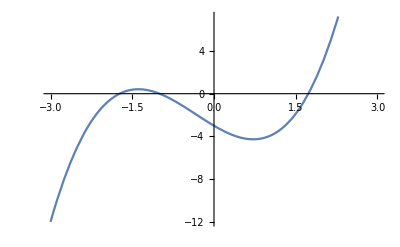

1    1.5    2.   -1.875

2    1.5    1.75   -1.875

3    1.625    1.75   -0.943359

4    1.6875    1.75   -0.409424

5    1.71875    1.75   -0.124786

Root = 1.73438

```mathematica
bisection[f_, a0_, b0_, n_]:= Module[{}, a = N[a0];b = N[b0];If[f[a]*f[b] > 0, Print["bisection method can not be applied"];
Return[]];
p = (a+b)/2;
i=1;
While[i ≤ n, 
If[f[a]*f[p]<0, b=p,a=p];
Print[i, "    ", a, "    ", b, "   ",f[a]];
i++;
p = (a+b)/2];
Print["  Root = ", p]]
f[x_]:= x^3+x^2-3*x-3;
Plot[f[x],{x,-3,3}]
bisection[f,1,2,5]
```

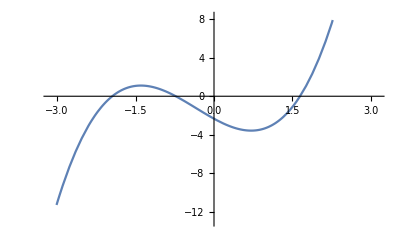

1    1.5    2.   -1.875

2    1.5    1.75   -1.875

3    1.625    1.75   -0.943359

4    1.6875    1.75   -0.409424

5    1.71875    1.75   -0.124786

Root = 1.73438

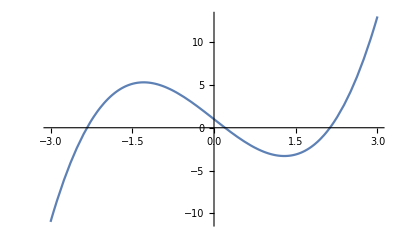

1    0.    0.5

2    0.    0.25

3    0.125    0.25

4    0.1875    0.25

5    0.1875    0.21875

Root = 0.203125

```mathematica
f[x_]  = x^3-5x+1;
Plot[f[x], {x, -3, 3}]
bisection[f, 0,1,5]
```

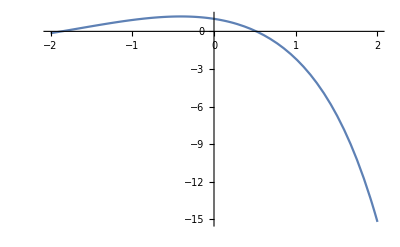

1    0.5    1.

2    0.5    0.75

3    0.5    0.625

4    0.5    0.5625

5    0.5    0.53125

Root = 0.515625

```mathematica
f[x_]=Cos[x]-x*Exp[x];
Plot[f[x], {x, -2,2}]
bisection[f,0,1,5]
```